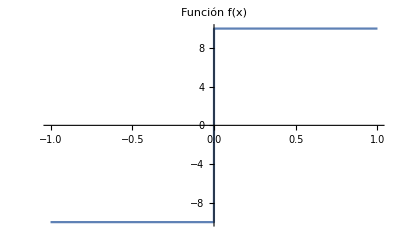

```mathematica
Plot[Piecewise[{{-10, x<0},{10,x<1}}],{x, -1,1}, PlotLabel->Style["Función f(x)", FontSize->16]]
```

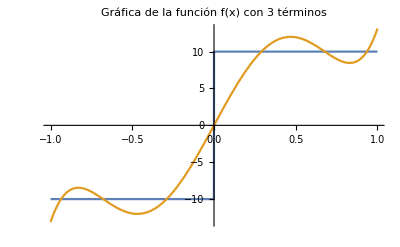

```mathematica
Plot[{Piecewise[{{-10, x<0},{10,x<1}}],10*((3/2)LegendreP[1,x]- (7/8)LegendreP[3,x]+(11/16) LegendreP[5,x])},{x,-1,1} ,PlotLabel->Style["Gráfica de la función f(x) con 3 términos", FontSize->16]]
```

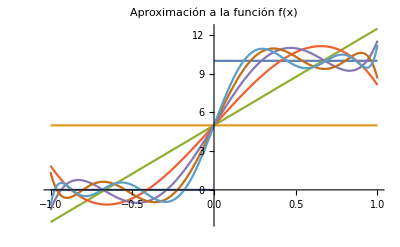

```mathematica
f[x_]:=10*UnitStep[x]
a[m_,f_]:=a[m,f]=(2 m+1)/2 Integrate[LegendreP[m,x] f[x],{x,-1,1}]
k=Sum[a[m,f] LegendreP[m,#],{m,0,i}]&;
Plot[Evaluate@Join[{f[t]},Table[k[t]*10,{i,0,10,2}]],{t,-1,1},PlotRange->All, PlotLabel->Style["Aproximación a la función f(x)", FontSize->16]]
```